```mathematica
g[n_,k_,a_]:=Sum[ ((-1)^(m+1))^(k-j) Binomial[k,j] g[Floor[n/m^(k-j)],j,m+1],{m,a,n^(1/k)},{j,0,k-1}];
g[n_,1,a_]:=((-1)^(n+1)+(-1)^(a+1))/2
g[n_,0,a_]:=1
LAdd[n_] := Sum[ 2^k/k,{k,1,Log[2,n]}]
LinE[n_] := LAdd[n] + Sum[ (-1)^(k+1)/k g[n,k,2],{k,1,Log[2,n]}]
```

```mathematica
LinE[101]
```

443/15

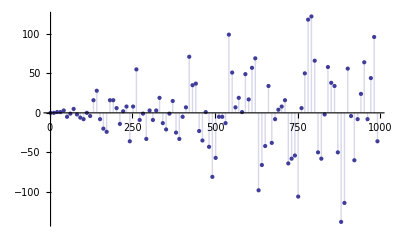

```mathematica
DiscretePlot[ g[n,4,2],{n,2,1000,10}]
```

```mathematica
E1[n_,k_,x_]:=Sum[E1[n/j,k-1,x],{j,1,n}]-x Sum[E1[n/(x j),k-1,x],{j,1,n/x}];E1[n_,0,x_]:=1
E1a[ n_, x_] := Sum[ 1, {j,1,n},{k,1,n/j}] - x Sum[ 1, {j,1,n}, {k,1,n/(j x)}] - x Sum[ 1, {j,1,n/x}, {k,1,n/(j x)}] + x^2 Sum[ 1, {j,1,n/x},{k,1,n/(j x x)}]
E1b[ n_, x_] := Sum[ 1, {j,1,n},{k,1,n/j}] - 2 x Sum[ 1, {j,1,n}, {k,1,n/(j x)}] + x^2 Sum[ 1, {j,1,n/x},{k,1,n/(j x x)}]
E2[n_,k_,x_]:=Sum[E2[n/j,k-1,x],{j,2,n}]-x Sum[E2[n/(x j),k-1,x],{j,1,n/x}];E2[n_,0,x_]:=1
E2a[ n_, x_] := Sum[ 1, {j,2,n},{k,2,n/j}] - x Sum[ 1, {j,2,n}, {k,1,n/(j x)}] - x Sum[ 1, {j,1,n/x}, {k,2,n/(j x)}] + x^2 Sum[ 1, {j,1,n/x},{k,1,n/(j x x)}]
E2b[ n_, x_] := Sum[ 1, {j,2,n},{k,2,n/j}] - 2 x Sum[ 1, {j,2,n}, {k,1,n/(j x)}] + x^2 Sum[ 1, {j,1,n/x},{k,1,n/(j x x)}]
```

```mathematica
E1[217,2,1.07]
```

10.3927

```mathematica
E1a[217,1.07]
```

10.3927

```mathematica
E1b[217,1.07]
```

10.3927

```mathematica
E2[217,2,1.07]
```

9.6727

```mathematica
E2a[217,1.07]
```

9.6727

```mathematica
E2b[217,1.07]
```

9.6727